```mathematica
Quit[]
```

```mathematica
$Assumptions=α∈Reals&&α>0&&m∈Reals&&m>0&&λ∈Reals;
```

```mathematica
ω[p_]:=√(m^2+p^2);Nx=100;
```

```mathematica
α=1;
```

```mathematica
ϕ[n_][p_]:=√(α/(√π 2^n n!)) HermiteH[n,α p] E^(1/2 (-α^2) p^2)
```

```mathematica
H[n_]:=ω[p]ϕ[n][p]-λ First@Integrate[(ϕ[n][k]-ϕ[n][p])/(p-k)^2,{k,-∞,∞},PrincipalValue->True]
```

```mathematica
Integrate[ϕ[0][p]ω[p]ϕ[0][p],{p,-∞,∞}]-λ Integrate[ϕ[0][p](ⅇ^(-1/2 p^2 α^2) √α (-ⅇ^((p^2 α^2)/2) √(2 π) √(α^2)+p α (π √(α^2) Erfi[(p α)/(√2)]-α (Log[-1/p]+Log[p]))))/π^(1/4),{p,-∞,∞}]
```

√π α λ+HypergeometricU[-1/2,0,m^2 α^2]/α

```mathematica
Integrate[ϕ[0][p]H[0],{p,-∞,∞}(*,PrincipalValue->True,GenerateConditions->False*)]//Timing
```

{15.0938,√π α λ+HypergeometricU[-1/2,0,m^2 α^2]/α}

```mathematica
Table[Integrate[ϕ[i][p]H[n],{p,-∞,∞}],{i,0,Nx},{n,0,Nx}]
```

Integrate::fas: Warning: one or more assumptions evaluated to False.

$Aborted

```mathematica
Integrate[ϕ[1][p]ω[p]ϕ[0][p],{p,-∞,∞}]
```

ConditionalExpression[0,Re[α^2]>0]

```mathematica
Integrate[(ϕ[0][k]-ϕ[0][p])/(p-k)^2,{k,-∞,∞},PrincipalValue->True]
```

ConditionalExpression[(ⅇ^(-1/2 p^2 α^2) √α (-ⅇ^((p^2 α^2)/2) √(2 π) Abs[α]+p α^2 (π Erfi[(p Abs[α])/(√2)]-Log[-1/p]+Log[1/p])))/π^(1/4),Im[p]≠0||Re[p]==0]

```mathematica
First@%6
```

(ⅇ^(-1/2 p^2 α^2) √α (-ⅇ^((p^2 α^2)/2) √(2 π) √(α^2)+p α (π √(α^2) Erfi[(p α)/(√2)]-α (Log[-1/p]+Log[p]))))/π^(1/4)

```mathematica
FullSimplify@((ⅇ^(-1/2 p^2 α^2) √α (-ⅇ^((p^2 α^2)/2) √(2 π) √(α^2)+p α (π √(α^2) Erfi[(p α)/(√2)]-α (Log[-1/p]+Log[p]))))/π^(1/4))/.α->1
```

```mathematica
Integrate[ϕ[0][p](ⅇ^(-p^2/2) (-ⅇ^(p^2/2) √(2 π)+p (π Erfi[p/(√2)]-Log[-1/p]-Log[p])))/π^(1/4),{p,-∞,∞}]
```

ConditionalExpression[-(2 √π √α √(α^2))/(1+α^2),Re[α^2]>0]

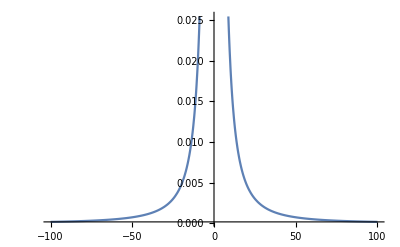

```mathematica
Plot[(ⅇ^(-p^2/2) (-ⅇ^(p^2/2) √(2 π)+p (π Erfi[p/(√2)]-Log[-1/p]-Log[p])))/π^(1/4),{p,-100,100},PlotRange->All]
```

```mathematica
Integrate[((E^(-1/2 k^2 α^2) √α)/π^(1/4))/(-k+p)^2,{k,-∞,∞},PrincipalValue->True]
```

ConditionalExpression[(ⅇ^(-1/2 p^2 α^2) √α (-ⅇ^((p^2 α^2)/2) √(2 π) √(α^2)+p α (π √(α^2) Erfi[(p α)/(√2)]-α (Log[-1/p]+Log[p]))))/π^(1/4),(Re[p]==0||p∉Reals)&&Re[α^2]≥0]